# DD Calculation ala Fitzpatrick et al.

## Initials

```mathematica
(*ResourceFunction["MaTeXInstall"][]*)
<<MaTeX`;

rasterTrick[plot_]:=
Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]

frametrick[plt_]:=Show[plt,GridLines->Automatic,(*GridLinesStyle->{{Dashed,Thin,Gray},{Dashed,Thin,Gray}},*)Frame->True,FrameStyle->
{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
LabelStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"](*{FontSize->12,Black}*)]

frametricknogrid[plt_]:=Show[plt,Frame->True,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
LabelStyle->Directive[FontSize->16,FontColor->Black,FontFamily->"Times New Roman"]]


(* to automatically save as a mathematica data file*)
SaveIt[filename_,varnamestring_]:=Module[{output},
output=Export[datadir<>"/"<>filename<>".dat", ToString[ToExpression[varnamestring]//InputForm], "String"];
output
];

ReadIt[filename_]:=Module[{output},
output=ToExpression[Import[datadir<>"/"<>StringReplace[filename,".dat"->""]<>".dat", "String"]];
output
];



(*https://mathematica.stackexchange.com/questions/33206/implementation-of-smoothing-splines-function/89148#89148*)
SmoothingSplineFunction[dat_?MatrixQ,p:(_?NumericQ|Automatic):Automatic]:=Module[{n=Length[dat],pv=p,cc,dc,del,h,qg,qm,rh,tm,uv,xa,ya},{xa,ya}=Transpose[dat];h=Differences[xa];rh=1/h;
del=Differences[ya] rh;
qm=SparseArray[{Band[{1,1}]->Most[rh],Band[{1,2}]->-ListCorrelate[{1,1},rh],Band[{1,3}]->Rest[rh]},{n-2,n}];
tm=SparseArray[{Band[{2,1}]->Most[Rest[h]],Band[{1,1}]->ListCorrelate[{2,2},h],Band[{1,2}]->Drop[h,-2]},{n-2,n-2}];
qg=qm.Transpose[qm];
If[pv===Automatic,pv=1/(1+Tr[tm]/(6 Tr[qg]))];
uv=LinearSolve[6 (1-pv) qg+pv tm,Differences[del]];
dc=ya-6 (1-pv) Differences[ArrayPad[Differences[ArrayPad[uv,1]]/h,1]];
Interpolation[Transpose[{List/@xa,dc,Append[Differences[dc]/h-h ListCorrelate[{2,1},ArrayPad[pv uv,1]],pv Last[uv] Last[h]-(Subtract@@Take[dc,-2])/Last[h]]}],InterpolationOrder->3,Method->"Hermite"]]

plotdir = FileNameJoin[{NotebookDirectory[],"figures" }];
datadir = NotebookDirectory[]<>"data/" ;
```

Get::noopen: Cannot open MaTeX`.

```mathematica
cval=3 10^8;
gstoday=2.7;
Teq=10^-9(*GeV*);
T0=2.72 8.62 10^-14;
Mpl=2.394 10^18 √(8π)(*Mpl*)(*1.2 10^19*)(*This is what Kolb&Turner and Gorbunov all use.*)(*GeV*);
Gconstant=1/Mpl^2;

S0OVREρ0=2890/(1.05 10^-5)(*GeV^-1*);

mu=4 10^-3;
md=8 10^-3;
mt=172;
mτ=1.77682;
me=0.511 10^-3;
mμ=0.105658;
mb=4.18;
mc=1.275;
ms=0.1;
mlepton={me,mμ,mτ};
mqup={mu,mc,mt};
mqdown={md,ms,mb};

αs=0.118;

(*mDstar=2.010268;*)Vcb=0.0405;Vts=0.0404;Vcd=0.22;Vcs=0.987;Vub=0.004;Vud=0.9737;Vus=0.2245;Vtd=0.008;Vtb=1.013;
mZ=91.1876;
sw=√0.23;
αem=7.2973525664*10^(-3);
αw=αem/sw^2;
hvev=246;
clight=3 10^8(*m/sec*);
GevJ=1.6 10^-10;

hbar=QuantityMagnitude[UnitConvert[Quantity[, "ReducedPlanckConstant"],"GeV" "s"]](*GeV*) (*sec*);
mjpsi=3.097;

GF=1.1663787 10^-5(*GeV^-2*);



mB=5.27926;
mBs=5.367;
mBc=6.275;
mD=1.86959;
mDs=1.968;
mπ=0.140;
mK=0.494;
(*charged fP*)
fBc = 0.434 (*GeV*);
fD=0.049/Vcd(*GeV*);
fDs=0.252/Vcs(*GeV*);
fK=0.156;
fπ=0.130;
fB=0.190;

(*neutral*)
fBs=0.227;

(*τ charged in GeV^-1*)
τB=1.638 10^-12 1/hbar;
τDs=504 10^-15 1/hbar;
τD=1033 10^-15 1/hbar;
τπ=2.60 10^-8 1/hbar;
τK=1.238 10^-8 1/hbar;
τBc = 0.510 10^-12 1/hbar;

τBs=1.52 10^-12 1/hbar;
mw=80.385;
```

## Basic functions and quantities

The following integral takes a little bit.

```mathematica
avgv=√(vss^2+vpp^2+vss vpp Cos[(2π)/T t]);
(*avgvexp=Assuming[vpp>0&&vss>vpp&&T>0,1/T Integrate[avgv,{t,0,T}]//Simplify]*)

avgvexp = (√(vpp^2-vpp vss+vss^2) EllipticE[-(2 vpp vss)/(vpp^2-vpp vss+vss^2)]+√(vpp^2+vpp vss+vss^2) EllipticE[(2 vpp vss)/(vpp^2+vpp vss+vss^2)])/π
```

(√(vpp^2-vpp vss+vss^2) EllipticE[-(2 vpp vss)/(vpp^2-vpp vss+vss^2)]+√(vpp^2+vpp vss+vss^2) EllipticE[(2 vpp vss)/(vpp^2+vpp vss+vss^2)])/π

```mathematica
(*velocity and masses and kinematics from Del Nobile*)
mN=0.939(*GeV*);


mred[m1_,m2_]:=(m1 m2)/(m1 + m2)
vmin[ER_,mtar_,mdm_]:=√((mtar ER)/(2(mred[mdm,mtar])^2))
qfunc[er_,mtar_]:=√(2 mtar er)

qang[er_,mass_] = qfunc[er,mass]  QuantityMagnitude[UnitConvert[Quantity[ 1,"GeV"]/(cqu hbarval),1/"Angstroms"]];

ΛBoverΛA = 2.5;

ρDM=0.3(*GeV/cm^3 - PDG*) (hbar cval 10^2(*GeV cm*))^3 (*"ρDM" is in GeV^4*);
(*by from Fitzpatrick appendix*)
by[An_]:=√(41.467/(45 An^(-1/3)-25 An^(-2/3)))(*fm*)(hbar cval 10^15(*GeV fm*))^-1 (*"by" is in GeV^-1*)
byDM[An_] := by[An]/ΛBoverΛA

yy[An_,er_,mtar_] := ((by[An] qfunc[er,mtar])/2)^2
yyDM[An_,er_,mtar_] := ((byDM[An] qfunc[er,mtar])/2)^2

(*Following from Kavanagh appendix*)
gN[p]=5.59;
gN[n]=-3.83;
Qch[p]=1;
Qch[n]=0;
```

```mathematica
days=60;detectorton=5.5;
mudm[mdm_] :=  -1.9  (√(4π αem))/(2 mdm) 
mdarkneutron =5; (*GeV*)
mdarkhelium = 20 ; 
Qneutron = 0;
Qhelium = 2; (* ionized *)


kappa = 10^-9;

UnitConvert[Quantity[detectorton,"ton"],"kg"]
```

4989.52 kg

Velocity - angular integration:
I.36 of Del Nobile sets up angular integration: H= v f(v) from dRT/dET integral

```mathematica
(* standard halo model*)
(* vesc is hard coded into this*)

vesc=((*800*)(*580*)544 10^3)/cval;(* hard coded into following equations, other quantities are replaceable*)
vs=(232 10^3)/cval//N;
vplus=(30 10^3)/cval;
vc=(220 10^3)/cval//N;
v0=vc;
vEavg= avgvexp/.{vss->vs,vpp->vplus}//N;
(*is same as vs*)
Nesc[v0_]:=Erf[vesc/v0]-2/(3 √π)vesc/v0(3(*+2β vesc^2/v0^2*))ⅇ^(- vesc^2/v0^2)(*/.{β->0}*)//N
costhetamax[v_,vE_] :=(vesc^2-v^2-vE^2)/(2 v vE)

vpm ["plus",mdm_,ER_,labelT_,vavg_]:= Min[vmin[ER,mT[labelT],mdm],vesc+vavg]
vpm ["minus",mdm_,ER_,labelT_,vavg_]:= Min[vmin[ER,mT[labelT],mdm],vesc-vavg]
fSHM[v_,vavg_,cth_,vo_,Nes_]:=(ⅇ^(-(v^2+vavg^2+2v vavg cth)/vo^2))/((vo √π)^3 Nes);
(*angularintminus[v_,vavg_,vo_,Nes_]=2π Integrate[fSHM[v ,vavg,cth,vo,Nes],
{cth,-1,costhetamax [v,vavg]}]//Simplify*)

angularintminus[v_,vavg_,vo_,Nes_] =(-ⅇ^(-289/(87890625 vo^2))+ⅇ^(-(v-vavg)^2/vo^2))/(Nes √π v vavg vo);
(*
angularintplus[v_,vavg_,vo_,Nes_]=2π Integrate[fSHM[v ,vavg,cth,vo,Nes],
{cth,1,costhetamax [v,vavg]}]//Simplify 
*)
angularintplus[v_,vavg_,vo_,Nes_]=(-ⅇ^(-289/(87890625 vo^2))+ⅇ^(-(v+vavg)^2/vo^2))/(Nes √π v vavg vo);

FE1D[v_,vavg_,vo_] := (HeavisideTheta[vesc+vavg-v] v^2 angularintminus[v,vavg,vo,Nesc[vo]] 
- HeavisideTheta[vesc-vavg-v] v^2 angularintplus[v,vavg,vo,Nesc[vo]] )
```

```mathematica
angularintminushalo[v_]=angularintminus[v,vEavg,v0,Nesc[v0]]//Simplify

angularintplushalo[v_]=angularintplus[v,vEavg,v0,Nesc[v0]]//Simplify 

vpmhalo[x_,mdm_,ER_,labelT_]= vpm[x,mdm,ER,labelT, vEavg];

FE1Dhalo[v_] := (HeavisideTheta[ves+ve-v] v^2 angularintminushalo[v] 
- HeavisideTheta[ves-ve-v] v^2 angularintplushalo[v] )/. {ves->vesc, ve-> vEavg}


"check that the normalization has worked right"
Integrate[FE1Dhalo[v],{v,0,1}] //N
```

(994237. (-0.00221085+ⅇ^(-1.8595×10^6 (-0.000778981+v)^2)))/v

(994237. (-0.00221085+ⅇ^(-1.8595×10^6 (0.000778981+v)^2)))/v

check that the normalization has worked right

1.

velocity integrals, these take a minute or so. Compute once and save the results

```mathematica
(* relevant integrals over distribution are f/v and vf, precompute*)
(*Timing[η0[ER_,labelT_,mdm_] = Assuming[ER>=0 && mdm>= 0 && mT[labelT]>=0, Integrate[ FE1Dhalo[v]/v,{v,vmin[ER,mT[labelT],mdm],1}]];
η1[ER_,labelT_,mdm_] = Assuming[ER>=0 && mdm>= 0 && mT[labelT]>=0, Integrate[v FE1Dhalo[v],{v,vmin[ER,mT[labelT],mdm],1}]];]

SaveIt["VelocityIntegral0","η0[ER,labelT,mdm]"]
SaveIt["VelocityIntegral1","η1[ER,labelT,mdm]"]*)

η0[ER_,labelT_,mdm_] = ReadIt["VelocityIntegral0"];
η1[ER_,labelT_,mdm_] = ReadIt["VelocityIntegral1"];
```

```mathematica
cval
```

300000000

```mathematica
(angularintminus[v, ve, vss, Nesc[vss]] /. ve->vEavgdisk//Simplify )/. vss-> vSdisk //Simplify
```

(-1.+ⅇ^(289/(87890625 vSdisk^2)-(v-vEavgdisk)^2/vSdisk^2))/(√π v vEavgdisk (-0.00204613+ⅇ^((3.28818×10^-6)/vSdisk^2) vSdisk Erf[0.00181333/vSdisk]))

```mathematica
(angularintminus[v,vEavgdisk,vss,Nesc[vss]]//Simplify) /. vss-> vSdisk //Simplify
```

(-1.+ⅇ^(289/(87890625 vSdisk^2)-(v-vEavgdisk)^2/vSdisk^2))/(√π v vEavgdisk (-0.00204613+ⅇ^((3.28818×10^-6)/vSdisk^2) vSdisk Erf[0.00181333/vSdisk]))

```mathematica
(* dark disk version, just rescaled speed parameters, no fancy machinery*)
Clear[vpmdisk, angularintminusdisk,angularintplusdisk,FE1Ddisk]

vSdisk = (20 10^3)/cval//N;
vEdisk = (30 10^3)/cval;
vEavgdisk= avgvexp/.{vss->vSdisk,vpp->vEdisk}//N;
vescdisk = vesc  ;

(* if you input both values at once get overflow errors, sequentially its fine*)
angularintminusdisk[v_]=(angularintminus[v,vEavgdisk,vss,Nesc[vss]]//Simplify) /. vss-> vSdisk //Simplify

angularintplusdisk[v_]=(angularintplus[v,vEavgdisk,vss,Nesc[vss]]//Simplify) /. vss-> vSdisk //Simplify

vpmdisk[x_,mdm_,ER_,labelT_]=vpm[x,mdm,Er,labelT, vEavgdisk];

FE1Ddisk[v_] := (HeavisideTheta[ves+ve-v] v^2 angularintminusdisk[v] 
				- HeavisideTheta[ves-ve-v] v^2 angularintplusdisk[v] )/. {ves->vesc, ve-> vEavgdisk}
				
"check normalization is behaving"				
Integrate[FE1Ddisk[v],{v,0,1}] //N
```

(-3.5106×10^-314+3.03203×10^6 ⅇ^((53323.5-2.25×10^8 v) v))/v

(-3.5106×10^-314+3.03203×10^6 ⅇ^((-53323.5-2.25×10^8 v) v))/v

check normalization is behaving

1.

## Nuclear Response

this section gives all the nuclear form factors for the target nuclei

```mathematica
(*translations between basis found in 1203.3542 eq 76*)
conversion[j_] := (4 π)/(2 j + 1);
FormFactorBasisConvert[functionlist_,labelT_,j_] := Do[
				conv = conversion[j];
				func[labelT][n,n][y_] = conv (func[labelT][0,0][y]-func[labelT][0,1][y]-func[labelT][1,0][y]+func[labelT][1,1][y]);
				func[labelT][p,p][y_] = conv (func[labelT][0,0][y]+func[labelT][0,1][y]+func[labelT][1,0][y]+func[labelT][1,1][y]);
				func[labelT][p,n][y_] = conv (func[labelT][0,0][y]-func[labelT][0,1][y]+func[labelT][1,0][y]-func[labelT][1,1][y]);
				func[labelT][n,p][y_] = conv (func[labelT][0,0][y]+func[labelT][0,1][y]-func[labelT][1,0][y]-func[labelT][1,1][y]);,
			{func,functionlist}]
```

### ξ and ζ: Data From Del Nobile Table 1

```mathematica
Znum["Xe"]= 54;
Znum["Ge"] = 32;
Znum["Si"] = 14;
Znum["He"] = 2;
isotopes["Xe"]={"Xe128","Xe129","Xe130","Xe131","Xe132","Xe134","Xe136"};
isotopes["Ge"] = {"Ge70","Ge72","Ge74","Ge76","Ge73"};
isotopes["Si"] = {"Si28"};
isotopes["He"] = {"He4"};

ξT["Xe128"]=0.019;Anum["Xe128"]=128;mT["Xe128"]=119;
ξT["Xe129"]=0.26;Anum["Xe129"]=129; mT["Xe129"]=120;
ξT["Xe130"]=0.041;Anum["Xe130"]=130; mT["Xe130"]=121;
ξT["Xe131"]=0.21;Anum["Xe131"]=131; mT["Xe131"]=122;
ξT["Xe132"]=0.27;Anum["Xe132"]=132; mT["Xe132"]=123;
ξT["Xe134"]=0.10;Anum["Xe134"]=134; mT["Xe134"]=125;
ξT["Xe136"]=0.089;Anum["Xe136"]=136; mT["Xe136"]=126;

ξT["Ge70"]=0.2;Anum["Ge70"]=70;mT["Ge70"]=65;
ξT["Ge72"]=0.27;Anum["Ge72"]=72;mT["Ge72"]=67;
ξT["Ge74"]=0.37; Anum["Ge74"]=4;  mT["Ge74"]=69; 
ξT["Ge76"]=0.078; Anum["Ge76"]=76; mT["Ge76"]=71; 
ξT["Ge73"]=0.078; Anum["Ge73"]=73; mT["Ge73"]=68;

ξT["Si28"]=0.92; Anum["Si28"]=28; mT["Si28"]=26;

ξT["He4"]=1;Anum["He4"]=4; mT["He4"]=4;

threshold["Xe"] = {6.6 10^-6,43.3 10^-6}; (*1207.5988*)
threshold["Ge"] =  {40 10^-9,43.3 10^-6 } ;(*1610.00006 table 8 Ge HV lower threshold, still need to get better number for upper thresh*)
threshold["Si"] =  {78 10^-9,43.3 10^-6 } ;

ζT[tar_,labelT_]:=(ξT[labelT]mT[labelT] )/Sum[ξT[l]mT[l],{l,isotopes[tar]}];
```

### [“Ge70”]

```mathematica
labelGe = "Ge70";

FM[labelGe][p,p][y_] := ⅇ^(-2y)(1000−2800y+2900 y^2−1400 y^3+350 y^4−42 y^5+1.9 y^6−0.0027 y^7)
FM[labelGe][p,n][y_] := ⅇ^(-2y)(1200−3500y+3800 y^2−2000 y^3+530 y^4−70 y^5+3.8 y^6−0.034 y^7)
FM[labelGe][n,p][y_]:=FM[labelGe][p,n][y]
FM[labelGe][n,n][y_] := ⅇ^(-2y)(1400−4300y+4900 y^2−2700 y^3+780 y^4−110 y^5+7.2 y^6−0.11 y^7+0.00052 y^8)

FΣp[labelGe][x_,z_][y_]:=0
FΣpp[labelGe][x_,z_][y_]:=0
FΔ[labelGe][x_,z_][y_]:=0

FΦpp[labelGe][p,p][y_]:=ⅇ^(-2y)(36−58y+32 y^2−6.8 y^3+0.51 y^4−0.0028 y^5)
FΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(25−45y+29 y^2−7.8 y^3+0.91 y^4−0.034 y^5)
FΦpp[labelGe][n,p][y_]:=FΦpp[labelGe][p,n][y]
FΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(18−35y+25 y^2−8.4 y^3+1.3 y^4−0.088 y^5+0.0021 y^6)

FMΦpp[labelGe][p,p][y_]:=ⅇ^(-2y) (−190+420y−330 y^2+110 y^3−17 y^4+1.0 y^5−0.0034 y^6)
FMΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(−140+320y−280 y^2+110 y^3−22 y^4+2.0 y^5−0.063 y^6)
FMΦpp[labelGe][n,p][y_]:=ⅇ^(-2y)(−230+520y−430 y^2+160 y^3−28 y^4+1.9 y^5−0.021 y^6)
FMΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(−160+400y−370 y^2+160 y^3−35 y^4+3.5 y^5−0.14 y^6+0.0010 y^7)

FΣpΔ[labelGe][x_,z_][y_]:=0
```

### [“Ge72”]

```mathematica
labelGe = "Ge72";

FM[labelGe][p,p][y_] := ⅇ^(-2y)(1000−2800y+3000 y^2−1500 y^3+400 y^4−51 y^5+2.6 y^6−0.0069 y^7)
FM[labelGe][p,n][y_] := ⅇ^(-2y)(1300−3700y+4100 y^2−2200 y^3+600 y^4−82 y^5+4.5 y^6−0.017 y^7)
FM[labelGe][n,p][y_]:=FM[labelGe][p,n][y]
FM[labelGe][n,n][y_] := ⅇ^(-2y)(1600−4800y+5600 y^2−3100 y^3+910 y^4−130 y^5+7.8 y^6−0.039 y^7)

FΣp[labelGe][x_,z_][y_]:=0
FΣpp[labelGe][x_,z_][y_]:=0
FΔ[labelGe][x_,z_][y_]:=0

FΦpp[labelGe][p,p][y_]:=ⅇ^(-2y)(68−110y+64 y^2−16 y^3+1.4 y^4−0.010 y^5)
FΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(6.9−13y+8.8 y^2−2.7 y^3+0.36 y^4−0.018 y^5)
FΦpp[labelGe][n,p][y_]:=FΦpp[labelGe][p,n][y]
FΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(0.71−1.5y+1.2 y^2−0.42 y^3+0.075 y^4−0.0063 y^5+0.00020 y^6)

FMΦpp[labelGe][p,p][y_]:=ⅇ^(-2y) (−260+580y−460 y^2+170 y^3−30 y^4+2.0 y^5−0.0094 y^6)
FMΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(−27+66y−60 y^2+26 y^3−5.6 y^4+0.58 y^5−0.023 y^6)
FMΦpp[labelGe][n,p][y_]:=ⅇ^(-2y)(−330+760y−650 y^2+250 y^3−47 y^4+3.4 y^5−0.020 y^6)
FMΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(−34+87y−83 y^2+38 y^3−8.7 y^4+0.96 y^5−0.040 y^6+0.00010 y^7)

FΣpΔ[labelGe][x_,z_][y_]:=0
```

### [“Ge74”]

```mathematica
labelGe = "Ge74";

FM[labelGe][p,p][y_] := ⅇ^(-2y)(1000.−2800.y+2900. y^2−1400. y^3+350. y^4−41. y^5+1.9 y^6−0.0033 y^7)
FM[labelGe][p,n][y_] := ⅇ^(-2y)(1300.−4000.y+4400. y^2−2400. y^3+660. y^4−91. y^5+5.4 y^6−0.070 y^7)
FM[labelGe][n,p][y_]:=FM[labelGe][p,n][y]
FM[labelGe][n,n][y_] := ⅇ^(-2y)(1800.−5500.y+6700. y^2−3900. y^3+1200. y^4−190. y^5+14. y^6−0.33 y^7+0.0023 y^8)

FΣp[labelGe][x_,z_][y_]:=0
FΣpp[labelGe][x_,z_][y_]:=0
FΔ[labelGe][x_,z_][y_]:=0

FΦpp[labelGe][p,p][y_]:=ⅇ^(-2y)(36.−57.y+32. y^2−7.0 y^3+0.55 y^4−0.0035 y^5)
FΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(26.−52.y+36. y^2−11. y^3+1.5 y^4−0.073 y^5+0.00023 y^6)
FΦpp[labelGe][n,p][y_]:=FΦpp[labelGe][p,n][y]
FΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(20.−45.y+38. y^2−15. y^3+2.9 y^4−0.27 y^5+0.0093 y^6)

FMΦpp[labelGe][p,p][y_]:=ⅇ^(-2y) (−190.+420.y−330. y^2+110. y^3−18. y^4+1.0 y^5−0.0042 y^6)
FMΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(−140.+360.y−330. y^2+150. y^3−32. y^4+3.4 y^5−0.13 y^6+0.00012 y^7)
FMΦpp[labelGe][n,p][y_]:=ⅇ^(-2y)(−250.+600.y−510. y^2+200. y^3−37. y^4+2.8 y^5−0.043 y^6+0.00012 y^7)
FMΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(−190.+500.y−510. y^2+250. y^3−62. y^4+7.6 y^5−0.39 y^6+0.0047 y^7)

FΣpΔ[labelGe][x_,z_][y_]:=0
```

### [“Ge76”]

```mathematica
labelGe = "Ge76";

FM[labelGe][p,p][y_] := ⅇ^(-2y)(1000.−2800.y+2900. y^2−1400. y^3+340. y^4−40. y^5+1.8 y^6−0.0024 y^7)
FM[labelGe][p,n][y_] := ⅇ^(-2y)(1400.−4200.y+4800. y^2−2600. y^3+730. y^4−100. y^5+6.5 y^6−0.11 y^7)
FM[labelGe][n,p][y_]:=FM[labelGe][p,n][y]
FM[labelGe][n,n][y_] := ⅇ^(-2y)(1900.−6300.y+7800. y^2−4700. y^3+1500. y^4−260. y^5+21. y^6−0.66 y^7+0.0069 y^8)

FΣp[labelGe][x_,z_][y_]:=0
FΣpp[labelGe][x_,z_][y_]:=0
FΔ[labelGe][x_,z_][y_]:=0

FΦpp[labelGe][p,p][y_]:=ⅇ^(-2y)(31.−49.y+27. y^2−5.8 y^3+0.44 y^4−0.0024 y^5)
FΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(39.−78.y+54. y^2−17. y^3+2.3 y^4−0.11 y^5+0.00031 y^6)
FΦpp[labelGe][n,p][y_]:=FΦpp[labelGe][p,n][y]
FΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(50.−120.y+100. y^2−41. y^3+8.1 y^4−0.77 y^5+0.027 y^6)

FMΦpp[labelGe][p,p][y_]:=ⅇ^(-2y) (−180.+390.y−300. y^2+100. y^3−16. y^4+0.89 y^5−0.0030 y^6)
FMΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(−230.+580.y−550. y^2+240. y^3−53. y^4+5.5 y^5−0.22 y^6+0.00015 y^7)
FMΦpp[labelGe][n,p][y_]:=ⅇ^(-2y)(−240.+590.y−520. y^2+210. y^3−38. y^4+3.0 y^5−0.061 y^6+0.00015 y^7)
FMΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(−310.+870.y−910. y^2+460. y^3−120. y^4+15. y^5−0.85 y^6+0.014 y^7)

FΣpΔ[labelGe][x_,z_][y_]:=0
```

### [“Ge73”]

```mathematica
labelGe = "Ge73";

FM[labelGe][p,p][y_] := ⅇ^(-2y)(1000−2800y+2900 y^2−1500 y^3+380 y^4−47 y^5+2.3 y^6−0.0058 y^7)
FM[labelGe][p,n][y_] := ⅇ^(-2y)(1300−3800y+4200 y^2−2300 y^3+630 y^4−88 y^5+5.1 y^6−0.050 y^7)
FM[labelGe][n,p][y_]:=FM[labelGe][p,n][y]
FM[labelGe][n,n][y_] := ⅇ^(-2y)(1700−5200y+6100 y^2−3500 y^3+1100 y^4−160 y^5+11 y^6−0.17 y^7+0.0012 y^8)

FΣp[labelGe][p,p][y_]:= ⅇ^(-2y)(0.00020−0.00046y+0.0015 y^2−0.0023 y^3+0.0021 y^4−0.00076 y^5+0.00010 y^6)
FΣp[labelGe][p,n][y_]:= ⅇ^(-2y)(0.012−0.053y+0.072 y^2−0.067 y^3+0.038 y^4−0.012 y^5+0.0018 y^6−0.00014 y^7)
FΣp[labelGe][n,p][y_]:= FΣp[labelGe][p,n][y]
FΣp[labelGe][n,n][y_]:= ⅇ^(-2y)(0.74−4.7y+12. y^2−13. y^3+6.9 y^4−2.1 y^5+0.35 y^6−0.031 y^7+0.0019 y^8)

FΣpp[labelGe][p,p][y_]:= ⅇ^(-2y)(0.00010−0.00096y+0.0034 y^2−0.0036 y^3+0.0020 y^4−0.00046 y^5)
FΣpp[labelGe][p,n][y_]:= ⅇ^(-2y)(0.0061−0.039y+0.058 y^2−0.054 y^3+0.026 y^4−0.0065 y^5+0.00082 y^6)
FΣpp[labelGe][n,p][y_]:= FΣpp[labelGe][p,n][y]
FΣpp[labelGe][n,n][y_]:= ⅇ^(-2y)(0.37−1.2y+2.3 y^2−2.0 y^3+1.0 y^4−0.30 y^5+0.057 y^6−0.0060 y^7+0.00095 y^8)

FΔ[labelGe][p,p][y_]:=ⅇ^(-2y)(0.0069−0.012y+0.0089 y^2−0.0031 y^3+0.00048 y^4)
FΔ[labelGe][p,n][y_]:=ⅇ^(-2y)(0.14−0.30y+0.25 y^2−0.099 y^3+0.018 y^4−0.0013 y^5)
FΔ[labelGe][n,p][y_]:=FΔ[labelGe][p,n][y]
FΔ[labelGe][n,n][y_]:=ⅇ^(-2y)(3.0−7.2y+6.9 y^2−3.1 y^3+0.72 y^4−0.080 y^5+0.0036 y^6)

FΦpp[labelGe][p,p][y_]:=ⅇ^(-2y)(51.−83.y+47. y^2−11. y^3+0.97 y^4−0.0073 y^5)
FΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(18.−34.y+24. y^2−7.2 y^3+0.99 y^4−0.049 y^5+0.00021 y^6)
FΦpp[labelGe][n,p][y_]:=FΦpp[labelGe][p,n][y]
FΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(6.6−15.y+13. y^2−5.5 y^3+1.1 y^4−0.12 y^5+0.0049 y^6)

FMΦpp[labelGe][p,p][y_]:=ⅇ^(-2y) (−230.+500.y−400. y^2+140. y^3−23. y^4+1.5 y^5−0.0076 y^6)
FMΦpp[labelGe][p,n][y_]:=ⅇ^(-2y)(−80.+200.y−190. y^2+85. y^3−19. y^4+2.1 y^5−0.089 y^6+0.00011 y^7)
FMΦpp[labelGe][n,p][y_]:=ⅇ^(-2y)(−290.+690.y−590. y^2+230. y^3−42. y^4+3.1 y^5−0.035 y^6+0.00011 y^7)
FMΦpp[labelGe][n,n][y_]:=ⅇ^(-2y)(−100.+270.y−280. y^2+130. y^3−33. y^4+4.0 y^5−0.20 y^6+0.0025 y^7)

FΣpΔ[labelGe][p,p][y_]:=ⅇ^(-2y)(−0.0012+0.0024y−0.0033 y^2+0.0023 y^3−0.00088 y^4+0.00015 y^5)
FΣpΔ[labelGe][p,n][y_]:=ⅇ^(-2y)(−0.025+0.058y−0.074 y^2+0.053 y^3−0.020 y^4+0.0036 y^5−0.00029 y^6)
FΣpΔ[labelGe][n,p][y_]:=ⅇ^(-2y)(−0.071+0.29y−0.38 y^2+0.24 y^3−0.075 y^4+0.011 y^5−0.00066 y^6)
FΣpΔ[labelGe][n,n][y_]:=ⅇ^(-2y)(−1.5+6.5y−10. y^2+7.1 y^3−2.6 y^4+0.49 y^5−0.048 y^6+0.0019 y^7)
```

### [Silicon ]

```mathematica
(* from 1501.03729; in isoscalar/isovector basis; conv accounts for different normalization*)

labelSi = "Si28";
j = 0;

FM[labelSi][0,0][y_] := 0.281695 ⅇ^(-2y)(7.44089 − 6.37784y + y^2)^2
FM[labelSi][0,1][y_] := 0
FM[labelSi][1,0][y_] := 0
FM[labelSi][1,1][y_] := 0

FΦpp[labelSi][0,0][y_] := 0.0739103 ⅇ^(-2y)(2.5 − y)^2
FΦpp[labelSi][0,1][y_] := 0
FΦpp[labelSi][1,0][y_] := 0
FΦpp[labelSi][1,1][y_] := 0

FMΦpp[labelSi][0,0][y_] := ⅇ^(-2y)(−2.68415 + 3.37434y − 1.281 y^2 + 0.144292 y^3)
FMΦpp[labelSi][0,1][y_] := 0
FMΦpp[labelSi][1,0][y_] := 0
FMΦpp[labelSi][1,1][y_] := 0

FormFactorBasisConvert[{FM,FΦpp,FMΦpp},labelSi,j]

FΣp[labelSi][x_,z_][y_]:=0
FΣpp[labelSi][x_,z_][y_]:=0
FΔ[labelSi][x_,z_][y_]:=0
FΣpΔ[labelSi][x_,z_][y_]:=0
```

### [“Xe128”]

```mathematica
labelXe="Xe128";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-11000 y^3+4200 y^4-950 y^5+120 y^6-7.8 y^7+0.20 y^8)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4000-15000y +24000 y^2-19000 y^3+8300 y^4-2100 y^5+320 y^6-25 y^7+0.85 y^8-0.0055 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(5500-23000y +38000 y^2-32000 y^3+16000 y^4-4600 y^5+790 y^6-75 y^7+3.3 y^8-0.041 y^9+0.00015 y^10)

FΣp[labelXe][x_,z_][y_]:=0
FΣpp[labelXe][x_,z_][y_]:=0
FΔ[labelXe][x_,z_][y_]:=0

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(180-440y +410 y^2-180 y^3+42 y^4-4.9 y^5+0.22 y^6)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(91-250y +270 y^2-140 y^3+40 y^4-6.2 y^5+0.48 y^6-0.014 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(44-140y +170 y^2-110 y^3+36 y^4-6.8 y^5+0.74 y^6-0.042 y^7+0.00095 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-730+2200y -2500 y^2+1500 y^3-450 y^4+76 y^5-6.4 y^6+0.21 y^7)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-360+1200y -1600 y^2+1100 y^3-390 y^4+81 y^5-9.5 y^6+0.57 y^7-0.014 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-1000+3300y -4200 y^2+2700 y^3-940 y^4+180 y^5-19 y^6+0.85 y^7-0.0058 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-490+1800y -2600 y^2+1900 y^3-780 y^4+190 y^5-25 y^6+1.9 y^7-0.060 y^8+0.00038 y^9)

FΣpΔ[labelXe][x_,z_][y_]:=0
```

### [“Xe130”]

```mathematica
labelXe="Xe130";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+4100 y^4-910 y^5+110 y^6-7.0 y^7+0.17 y^8)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4100-16000y +25000 y^2-19000 y^3+8600 y^4-2200 y^5+330 y^6-26 y^7+0.91 y^8-0.0076 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(5800-24000y +41000 y^2-36000 y^3+18000 y^4-5200 y^5+910 y^6-89 y^7+4.2 y^8-0.068 y^9+0.00034 y^10)

FΣp[labelXe][x_,z_][y_]:=0
FΣpp[labelXe][x_,z_][y_]:=0
FΔ[labelXe][x_,z_][y_]:=0

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(150-370y +330 y^2-150 y^3+34 y^4-3.8 y^5+0.17 y^6)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(120-350y +370 y^2-190 y^3+54 y^4-8.2 y^5+0.63 y^6-0.019 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(100-320y +390 y^2-240 y^3+80 y^4-15 y^5+1.7 y^6-0.094 y^7+0.0021 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-670+2000y -2300 y^2+1300 y^3-400 y^4+65 y^5-5.4 y^6+0.17 y^7)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-540+1800y -2400 y^2+1600 y^3-580 y^4+120 y^5-14 y^6+0.81 y^7-0.019 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-940+3100y -4000 y^2+2500 y^3-900 y^4+180 y^5-18 y^6+0.84 y^7-0.0075 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-760+2800y -4100 y^2+3000 y^3-1200 y^4+300 y^5-41 y^6+3.1 y^7-0.1 y^8+0.00085 y^9)

FΣpΔ[labelXe][x_,z_][y_]:=0
```

### [“Xe132”]

```mathematica
labelXe="Xe132";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+4000 y^4-880 y^5+110 y^6-6.4 y^7+0.15 y^8)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4200-17000y +26000 y^2-20000 y^3+9000 y^4-2300 y^5+340 y^6-27 y^7+0.98 y^8-0.0095 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(6100-26000y +44000 y^2-39000 y^3+20000 y^4-5900 y^5+1000 y^6-100 y^7+5.3 y^8-0.099 y^9+0.00061 y^10)

FΣp[labelXe][x_,z_][y_]:=0
FΣpp[labelXe][x_,z_][y_]:=0
FΔ[labelXe][x_,z_][y_]:=0

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(130-320y +290 y^2-130 y^3+29 y^4-3.2 y^5+0.14 y^6)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(150-430y +460 y^2-240 y^3+67 y^4-10 y^5+0.77 y^6-0.023 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(180-570y +700 y^2-430 y^3+140 y^4-27 y^5+3.0 y^6-0.17 y^7+0.0038 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-620+1900y -2100 y^2+1200 y^3-360 y^4+59 y^5-4.7 y^6+0.14 y^7)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-720+2400y -3200 y^2+2100 y^3-760 y^4+160 y^5-18 y^6+1 y^7-0.024 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-900+3000y -3800 y^2+2500 y^3-880 y^4+170 y^5-18 y^6+0.85 y^7-0.0092 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-1000+3900y -5700 y^2+4200 y^3-1700 y^4+420 y^5-59 y^6+4.5 y^7-0.16 y^8+0.0015 y^9)

FΣpΔ[labelXe][x_,z_][y_]:=0
```

### [“Xe134”]

```mathematica
labelXe="Xe134";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+3700 y^4-770 y^5+85 y^6-4.5 y^7+0.098 y^8-0.00028 y^9)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4300-17000y +27000 y^2-21000 y^3+9200 y^4-2300 y^5+340 y^6-26 y^7+0.93 y^8-0.011 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(6400-28000y +48000 y^2-43000 y^3+22000 y^4-6600 y^5+1200 y^6-120 y^7+6.6 y^8-0.15 y^9+0.0012 y^10)

FΣp[labelXe][x_,z_][y_]:=0
FΣpp[labelXe][x_,z_][y_]:=0
FΔ[labelXe][x_,z_][y_]:=0

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(80-190y +180 y^2-77 y^3+17 y^4-1.9 y^5+0.085 y^6-0.00064 y^7)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(180-490y +520 y^2-270 y^3+75 y^4-11 y^5+0.85 y^6-0.026 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(380-1200y +1500 y^2-910 y^3+310 y^4-59 y^5+6.3 y^6-0.35 y^7+0.0075 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-480+1500y -1700 y^2+920 y^3-270 y^4+41 y^5-3.1 y^6+0.094 y^7-0.00047 y^8)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-1100+3600y -4700 y^2+3000 y^3-1100 y^4+210 y^5-23 y^6+1.3 y^7-0.027 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-720+2400y -3100 y^2+2000 y^3-720 y^4+140 y^5-15 y^6+0.75 y^7-0.012 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-1600+5900y -8700 y^2+6500 y^3-2700 y^4+660 y^5-92 y^6+7.1 y^7-0.26 y^8+0.0030 y^9)

FΣpΔ[labelXe][x_,z_][y_]:=0
```

### [“Xe136”]

```mathematica
labelXe="Xe136";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+3700 y^4-770 y^5+85 y^6-4.5 y^7+0.097 y^8-0.00028 y^9)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4400-18000y +28000 y^2-22000 y^3+9700 y^4-2500 y^5+360 y^6-28 y^7+1 y^8-0.012 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(6700-30000y +51000 y^2-46000 y^3+24000 y^4-7300 y^5+1300 y^6-140 y^7+7.6 y^8-0.17 y^9+0.0014 y^10)

FΣp[labelXe][x_,z_][y_]:=0
FΣpp[labelXe][x_,z_][y_]:=0
FΔ[labelXe][x_,z_][y_]:=0

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(81-200y +180 y^2-78 y^3+17 y^4-1.9 y^5+0.088 y^6-0.00065 y^7)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(180-510y +540 y^2-280 y^3+78 y^4-12 y^5+0.90 y^6-0.028 y^7+0.00011 y^8)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(400-1300y +1600 y^2-960 y^3+320 y^4-62 y^5+6.7 y^6-0.38 y^7+0.0085 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-490+1500y -1700 y^2+930 y^3-270 y^4+42 y^5-3.2 y^6+0.095 y^7-0.00048 y^8)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-1100+3700y -4800 y^2+3100 y^3-1100 y^4+220 y^5-24 y^6+1.3 y^7-0.029 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-740+2500y -3300 y^2+2100 y^3-760 y^4+150 y^5-16 y^6+0.82 y^7-0.013 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-1600+6200y -9200 y^2+6900 y^3-2900 y^4+710 y^5-100 y^6+7.8 y^7-0.29 y^8+0.0034 y^9)

FΣpΔ[labelXe][x_,z_][y_]:=0
```

### [“Xe129”]

```mathematica
labelXe="Xe129";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+3900 y^4-840 y^5+98 y^6-5.6 y^7+0.12 y^8)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4000-16000y +24000 y^2-19000 y^3+8200 y^4-2100 y^5+300 y^6-23 y^7+0.77 y^8-0.0065 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(5600-24000y +39000 y^2-34000 y^3+17000 y^4-4900 y^5+850 y^6-82 y^7+3.9 y^8-0.065 y^9+0.00034 y^10)

FΣp[labelXe][p,p][y_]:=ⅇ^(-2y)(0.00042-0.0019y +0.0065 y^2-0.012 y^3+0.017 y^4-0.012 y^5+0.0041 y^6-0.00063 y^7)
FΣp[labelXe][p,n][y_]:=ⅇ^(-2y)(0.014-0.080y +0.23 y^2-0.41 y^3+0.43 y^4-0.24 y^5+0.070 y^6-0.010 y^7+0.00058 y^8)
FΣp[labelXe][n,p][y_]:=FΣp[labelXe][p,n][y]
FΣp[labelXe][n,n][y_]:=ⅇ^(-2y)(0.49-3.3y +8.8 y^2-12 y^3+9.8 y^4-4.5 y^5+1.2 y^6-0.16 y^7+0.010 y^8)

FΣpp[labelXe][p,p][y_]:=ⅇ^(-2y)(0.00021-0.0015y +0.0043 y^2-0.0063 y^3+0.0049 y^4-0.0020 y^5+0.00042 y^6)
FΣpp[labelXe][p,n][y_]:=ⅇ^(-2y)(0.0072-0.038y +0.082 y^2-0.097 y^3+0.068 y^4-0.027 y^5+0.0061 y^6-0.00073 y^7)
FΣpp[labelXe][n,p][y_]:=FΣpp[labelXe][p,n][y]
FΣpp[labelXe][n,n][y_]:=ⅇ^(-2y)(0.25-0.84y +1.4 y^2-1.5 y^3+0.94 y^4-0.37 y^5+0.089 y^6-0.012 y^7+0.00076 y^8)

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(130-300y +280 y^2-130 y^3+30 y^4-3.5 y^5+0.16 y^6)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(120-330y +360 y^2-190 y^3+55 y^4-8.4 y^5+0.64 y^6-0.019 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(120-360y +440 y^2-270 y^3+93 y^4-18 y^5+1.9 y^6-0.10 y^7+0.0021 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-610+1800y -2100 y^2+1200 y^3-360 y^4+59 y^5-4.8 y^6+0.14 y^7)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-580+2000y -2600 y^2+1700 y^3-600 y^4+120 y^5-14 y^6+0.76 y^7-0.016 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-840+2800y -3500 y^2+2300 y^3-810 y^4+160 y^5-17 y^6+0.78 y^7-0.0074 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-800+3000y -4300 y^2+3100 y^3-1300 y^4+310 y^5-42 y^6+3.1 y^7-0.10 y^8+0.00085 y^9)

FΔ[labelXe][p,p][y_]:=ⅇ^(-2y)(0.038-0.090y +0.091 y^2-0.048 y^3+0.014 y^4-0.0021 y^5+0.00012 y^6)
FΔ[labelXe][p,n][y_]:=ⅇ^(-2y)(-0.0041-0.012y +0.012 y^2+0.00056 y^3-0.0032 y^4+0.00062 y^5)
FΔ[labelXe][n,p][y_]:=FΔ[labelXe][p,n][y]
FΔ[labelXe][n,n][y_]:=ⅇ^(-2y)(0.00046+0.0038y +0.0091 y^2+0.0054 y^3-0.00062 y^5)

FΣpΔ[labelXe][p,p][y_]:=ⅇ^(-2y)(-0.0040+0.014y -0.033 y^2+0.040 y^3-0.024 y^4+0.0076 y^5-0.0011 y^6)
FΣpΔ[labelXe][p,n][y_]:=ⅇ^(-2y)(0.00044+0.00083y -0.0010 y^2+0.0067 y^3-0.00090 y^4-0.0018 y^5+0.00037 y^6)
FΣpΔ[labelXe][n,p][y_]:=ⅇ^(-2y)(-0.14+0.61y -1.1 y^2+0.95 y^3-0.47 y^4+0.13 y^5-0.019 y^6+0.0011 y^7)
FΣpΔ[labelXe][n,n][y_]:=ⅇ^(-2y)(0.015+0.012y -0.13 y^2+0.11 y^3+0.018 y^4-0.030 y^5+0.0050 y^6+0.00051 y^7-0.00012 y^8)
```

### [“Xe131”]

```mathematica
labelXe="Xe131";

FM[labelXe][p,p][y_]:=ⅇ^(-2y)(2900-11000y +15000 y^2-10000 y^3+3800 y^4-810 y^5+92 y^6-5.1 y^7+0.11 y^8)
FM[labelXe][p,n][y_]:=ⅇ^(-2y)(4200-16000y +25000 y^2-20000 y^3+8600 y^4-2200 y^5+310 y^6-24 y^7+0.83 y^8-0.0082 y^9)
FM[labelXe][n,p][y_]:=FM[labelXe][p,n][y]
FM[labelXe][n,n][y_]:=ⅇ^(-2y)(5900-25000y +43000 y^2-37000 y^3+19000 y^4-5500 y^5+980 y^6-97 y^7+4.9 y^8-0.096 y^9+0.00061 y^10)

FΣp[labelXe][p,p][y_]:=ⅇ^(-2y)(0.00012-0.00089y +0.0015 y^2+0.0015 y^3-0.00069 y^4-0.0012 y^5+0.00080 y^6-0.00016 y^7)
FΣp[labelXe][p,n][y_]:=ⅇ^(-2y)(0.0045-0.039y +0.095 y^2-0.038 y^3-0.077 y^4+0.087 y^5-0.035 y^6+0.0059 y^7-0.00035 y^8)
FΣp[labelXe][n,p][y_]:=FΣp[labelXe][p,n][y]
FΣp[labelXe][n,n][y_]:=ⅇ^(-2y)(0.18-1.6y +5.8 y^2-9.7 y^3+9.1 y^4-4.9 y^5+1.4 y^6-0.21 y^7+0.012 y^8)

FΣpp[labelXe][p,p][y_]:=ⅇ^(-2y)(0.00013 y^2-0.00062 y^3+0.00088 y^4-0.00053 y^5+0.00015 y^6)
FΣpp[labelXe][p,n][y_]:=ⅇ^(-2y)(0.0023+0.0032y -0.011 y^2-0.00077 y^3+0.019 y^4-0.018 y^5+0.0066 y^6-0.0011 y^7)
FΣpp[labelXe][n,p][y_]:=FΣpp[labelXe][p,n][y]
FΣpp[labelXe][n,n][y_]:=ⅇ^(-2y)(0.088+0.30y -0.23 y^2-0.47 y^3+1.2 y^4-1.1 y^5+0.44 y^6-0.086 y^7+0.0067 y^8)

FΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(100-250y +230 y^2-100 y^3+24 y^4-2.7 y^5+0.12 y^6)
FΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(150-400y +430 y^2-230 y^3+64 y^4-9.9 y^5+0.75 y^6-0.022 y^7)
FΦpp[labelXe][n,p][y_]:=FΦpp[labelXe][p,n][y]
FΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(200-640y +780 y^2-480 y^3+160 y^4-31 y^5+3.3 y^6-0.18 y^7+0.0038 y^8)

FMΦpp[labelXe][p,p][y_]:=ⅇ^(-2y)(-550+1700y -1900 y^2+1100 y^3-320 y^4+51 y^5-4.0 y^6+0.11 y^7)
FMΦpp[labelXe][p,n][y_]:=ⅇ^(-2y)(-770+2600y -3400 y^2+2200 y^3-790 y^4+160 y^5-17 y^6+0.96 y^7-0.021 y^8)
FMΦpp[labelXe][n,p][y_]:=ⅇ^(-2y)(-790+2600y -3400 y^2+2200 y^3-770 y^4+150 y^5-16 y^6+0.77 y^7-0.0086 y^8)
FMΦpp[labelXe][n,n][y_]:=ⅇ^(-2y)(-1100+4100y -5900 y^2+4400 y^3-1800 y^4+440 y^5-61 y^6+4.5 y^7-0.16 y^8+0.0015 y^9)

FΔ[labelXe][p,p][y_]:=ⅇ^(-2y)(0.022-0.054y +0.053 y^2-0.026 y^3+0.0071 y^4-0.00098 y^5)
FΔ[labelXe][p,n][y_]:=ⅇ^(-2y)(0.11-0.28y +0.31 y^2-0.19 y^3+0.062 y^4-0.010 y^5+0.00073 y^6)
FΔ[labelXe][n,p][y_]:=FΔ[labelXe][p,n][y]
FΔ[labelXe][n,n][y_]:=ⅇ^(-2y)(0.56-1.4y +1.8 y^2-1.3 y^3+0.51 y^4-0.11 y^5+0.0097 y^6-0.00015 y^7)

FΣpΔ[labelXe][p,p][y_]:=ⅇ^(-2y)(0.0016-0.0081y +0.0047 y^2+0.0049 y^3-0.0061 y^4+0.0023 y^5-0.00039 y^6)
FΣpΔ[labelXe][p,n][y_]:=ⅇ^(-2y)(0.0080-0.041y +0.027 y^2+0.020 y^3-0.038 y^4+0.020 y^5-0.0042 y^6+0.00032 y^7)
FΣpΔ[labelXe][n,p][y_]:=ⅇ^(-2y)(0.063-0.37y +0.72 y^2-0.68 y^3+0.35 y^4-0.098 y^5+0.014 y^6-0.00077 y^7)
FΣpΔ[labelXe][n,n][y_]:=ⅇ^(-2y)(0.31-1.9y +3.8 y^2-4.1 y^3+2.5 y^4-0.87 y^5+0.15 y^6-0.011 y^7)
```

### [“He3”]

```mathematica
(* from 1501.03729; in isoscalar/isovector basis; translations between basis found in 1203.3542 eq 76; conv accounts for different normalization*)

label = "He3";
j = 1/2;

FM[label][0,0][y_] := 0.358099 ⅇ^(-2y)
FM[label][0,1][y_] := 0.119366 ⅇ^(-2y)
FM[label][1,0][y_] := FM[label][0,1][y]
FM[label][1,1][y_] := 0.0397887 ⅇ^(-2y)

FΣpp[label][0,0][y_] :=0.0397887 ⅇ^(-2y)
FΣpp[label][1,1][y_] := FΣpp[label][0,0][y] 
FΣpp[label][0,1][y_] := -FΣpp[label][0,0][y] 
FΣpp[label][1,0][y_] := -FΣpp[label][0,0][y] 

FΣp[label][0,0][y_] :=0.0795775 ⅇ^(-2y)
FΣp[label][1,1][y_] := FΣpp[label][0,0][y] 
FΣp[label][0,1][y_] := -FΣpp[label][0,0][y] 
FΣp[label][1,0][y_] := -FΣpp[label][0,0][y] 

FormFactorBasisConvert[{FM,FΣpp,FΣp},label,conv]

FΔ[label][x_,z_][y_]:=0
FΣpΔ[label][x_,z_][y_]:=0
FΦpp[label][x_,z_][y_] := 0
FMΦpp[label][x_,z_][y_] := 0
```

### [“He4”]

```mathematica
labelHe = "He4";
j = 0;
FM[labelHe][0,0][y_] := 0.31831 ⅇ^(-2y)
FM[labelHe][0,1][y_] := 0
FM[labelHe][1,0][y_] := 0
FM[labelHe][1,1][y_] := 0

FΔ[labelHe][x_,z_][y_]:=0
FΣpΔ[labelHe][x_,z_][y_]:=0
FΦpp[labelHe][x_,z_][y_] := 0
FMΦpp[labelHe][x_,z_][y_] := 0
FΣp[labelHe][x_,z_][y_]:=0
FΣpp[labelHe][x_,z_][y_]:=0

FormFactorBasisConvert[{FM},labelHe,j]
```

## dσ_T/dE_R

MC 
del Nobile eq 8.6

```mathematica
dσTdER[labelT_]["MC"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:= (8 Pi mT[labelT])/(v^2 qfunc[er, mT[labelT]]^4)αem^2 Qdm^2 FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]

dσTdER[labelT_]["MC_He"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:= (8 Pi mT[labelT])/(v^2 qfunc[er, mT[labelT]]^4)αem^2 (FM["He4"][p,p][yyDM[Anum["He4"],er,mT[labelT]]] 
	FM[labelT][p,p][yy[Anum[labelT],er,mT[labelT]]])
```

MDM

```mathematica
dσTdER[labelT_]["MDM"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=(μdm/4)^2(((16αem)/er)(1-(mdm+2mT[labelT])/(2mdm mT[labelT] v^2)er)
	FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]
	+(αem mT[labelT])/(2 mN^2)1/v^2(16 FΔ[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2] 
	+ Sum[gN[N1]gN[N2](FΣp[labelT][N1,N2][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]
	 -8 Qch[N1]gN[N2] FΣpΔ[labelT][N1,N2][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2] ),{N1,{p,n}},{N2,{p,n}}]))

dσTdER[labelT_]["MDMSI"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=(μdm/4)^2(((16αem)/er)(1-(mdm+2mT[labelT])/(2mdm mT[labelT] v^2)er)
	FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2])

dσTdER[labelT_]["MDMSD"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=(μdm/4)^2((αem mT[labelT])/(2 mN^2)1/v^2 (16 FΔ[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2] 
	+ Sum[gN[N1]gN[N2](FΣp[labelT][N1,N2][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2] 
	-8 Qch[N1]gN[N2] FΣpΔ[labelT][N1,N2][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2] ),{N1,{p,n}},{N2,{p,n}}]))
```

CR

```mathematica
dσTdER[labelT_]["CR"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=((√(π αem)rsq)/3)^2(2αem mT[labelT])/v^2 FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]


dσTdER[labelT_]["CRscalar",WC_][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=WC^2(αem mT[labelT])/(2 v^2)FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]
```

MC + CR

```mathematica
dσTdER[labelT_]["MCCR"][er_,v_,mdm_,rsq_,μdm_,Qdm_]:=
	((2 mT[labelT] αem^2 Pi)/v^2)(rsq/3-(2 Qdm)/qfunc[er, mT[labelT]]^2)^2 FM[labelT][p,p][(qfunc[er,mT[labelT]]by[Anum[labelT]]/2)^2]
```

## Rates

### Velocity Averaged Cross Section

```mathematica
ClearAll[labelT, x]
labels ={"CR","MC","MDM","MDMSI","MDMSD","MDMCR","MCCR","MDM_muoff"};
(*labels = {"CR","MDM_muoff"};*)
ClearAll[g0,g1,vdσTdERavg, ser]
(* expand in a series in v, then use the precomputed velocity integrals *)
Do[ser = Series[dσTdER[labelT][labelOP][ER,1/x,mdm,rsq,μdm,Qdm],{x,0,4}];
	g0[labelOP,labelT_,ER_,mdm_,rsq_,μdm_,Qdm_] = SeriesCoefficient[ser,0];
	g1[labelOP,labelT_,ER_,mdm_,rsq_,μdm_,Qdm_] = SeriesCoefficient[ser,2];
	(*Print[labelOP," ",SeriesCoefficient[ser,2]]*)
	,{labelOP,labels}]
vdσTdERavg[labelT_][labelOP_][ER_,mdm_,rsq_,μdm_,Qdm_]:=( g1[labelOP,labelT,ER,mdm,rsq,μdm,Qdm]η0[ER,labelT,mdm]  
				+ g0[labelOP,labelT,ER,mdm,rsq,μdm,Qdm]η1[ER,labelT,mdm]);
```

### Rates

```mathematica
prefactordiff = QuantityMagnitude[UnitConvert[Quantity[ρDM,1/"GeV"] Quantity[clight,"m"/"s"]^2/Quantity[hbar,"GeV""s"],1/("kg" "GeV" "s")](3600 24 (*s/day*))];



dRTdEr[labelOp_,tar_,ER_][mdm_,rsq_,Qdm_,κ_]:= prefactordiff κ^2/mdm (
	Sum[ ζT[tar, labelT]/mT[labelT] vdσTdERavg[labelT][labelOp][ER,mdm,rsq,mudm[mdm],Qdm], {labelT,isotopes[tar]}])
```

```mathematica
(* acceptance rate from 1207.5988 *)
data = Import[FileNameJoin[{datadir,"acceptance.csv"}]];
(*data[[;;,1]]*=10^-6*)
acceptancerate = SmoothingSplineFunction[data, 0.9]; (* in keV, breaks when put in GeV*)
(*Show[ListPlot[data,PlotRange->All],Plot[f[x],{x,3 ,50 },PlotRange->All]]*)
```

```mathematica
(* for some reason, getting the integrated rate is way faster when seperating the two components of the velocity integral rather than integrating ER over the precomputed velocity integrals*)

RTintegratedgen[labelOp_,tar_][mdm_,rsq_,Qdm_,κ_,vavg_,vo_]:= prefactordiff κ^2/mdm(
	Sum[ζT[tar,labelT]/mT[labelT](NIntegrate[v v^2 angularintminus[v,vavg,vo,Nesc[vo]](*acceptancerate[ER*10^6]*)
							dσTdER[labelT][labelOp][ER,v,mdm,rsq,mudm[mdm],Qdm],
							{ER,threshold[tar][[1]],threshold[tar][[2]]},
							{v,vpm["plus",mdm,ER,labelT,vavg],vesc+vavg} ,AccuracyGoal->20]
					
					-NIntegrate[v v^2 angularintplus[v,vavg,vo,Nesc[vo]](*acceptancerate[ER*10^6]*)
							dσTdER[labelT][labelOp][ER,v,mdm,rsq,mudm[mdm],Qdm],
							{ER,threshold[tar][[1]],threshold[tar][[2]]},
							{v,vpm["minus",mdm,ER,labelT,vavg],vesc-vavg} ,AccuracyGoal->20]),
					{labelT,isotopes[tar]}])
	
RTintegratedhalo[labelOp_,tar_][mdm_,rsq_,Qdm_,κ_]:=RTintegratedgen[labelOp,tar][mdm,rsq,Qdm,κ,vEavg,v0]
RTintegrateddisk[labelOp_,tar_][mdm_,rsq_,Qdm_,κ_]:=RTintegratedgen[labelOp,tar][mdm,rsq,Qdm,κ,vEavgdisk,vSdisk]
 
mtest = 2.5;
Timing[RTintegratedgen["MC","Ge"][mtest,rsquare["lattice",mtest],Qhelium,kappa,vEavg,v0]]
```

{0.5625,151.302}

## Rate Spectrum

### Velocity Distributions

```mathematica
mtest = 5;
Table[{tar,"halo",Integrate[ FE1Dhalo[v]/v,{v,vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],mtest],1}] //N, "disk",
Integrate[ FE1Ddisk[v]/v,{v,vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],mtest],1}] //N},{tar,{"Ge","Si","Xe"}}]

Table[{tar,vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],5]*cval/10^3//N},{tar,{"Ge","Si","Xe"}}]
```

{{Ge,halo,1061.56,disk,29.6324},{Si,halo,1063.96,disk,41.6737},{Xe,halo,0.,disk,0.}}

{{Ge,73.6729},{Si,72.0375},{Xe,1238.96}}

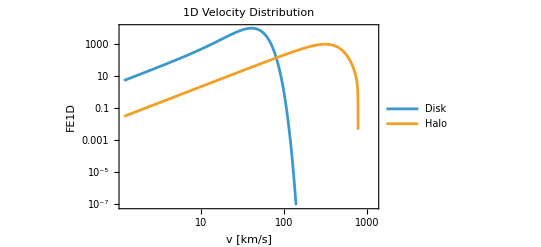

Halo

0.999562

Disk

0.864325

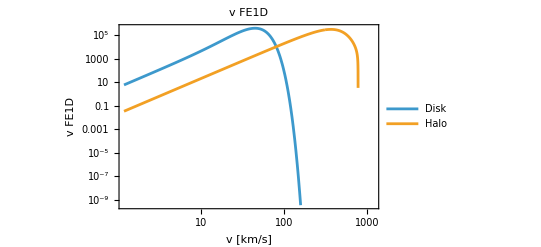

Halo

0.00110206

Disk

0.000127444

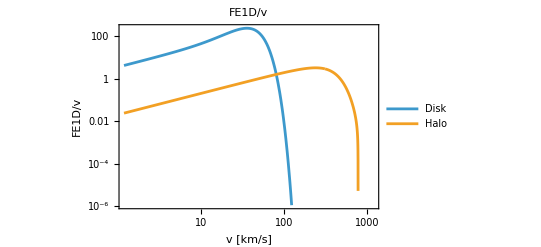

Halo

1109.58

Disk

6191.71

```mathematica
LogLogPlot[{FE1Ddisk[v 10^3/cval],FE1Dhalo[v 10^3/cval]},{v,0,1200},PlotLegends->{"Disk","Halo"},
	GridLines->{(*√(3/2)vEavg,√(3/2)vEavgdisk,vesc*)Table[vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],mdarkhelium]*cval/10^3,{tar,{"Ge","Si","Xe"}}],None},
	Frame->True,FrameLabel->{"v [km/s]","FE1D"},PlotLabel->"1D Velocity Distribution"]//frametricknogrid
(*Export[FileNameJoin[{plotdir, "FE.pdf"}],%];*)

Print["Halo"]
Integrate[ FE1Dhalo[v],{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N
Print["Disk"]
Integrate[ FE1Ddisk[v],{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N

LogLogPlot[{v FE1Ddisk[v 10^3/cval],v FE1Dhalo[v 10^3/cval]},{v,0,1200},PlotLegends->{"Disk","Halo"},
	GridLines->{(*√(3/2)vEavg,√(3/2)vEavgdisk,vesc*)Table[vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],mdarkhelium]*cval/10^3,{tar,{"Ge","Si","Xe"}}],None},
	Frame->True,FrameLabel->{"v [km/s]","v FE1D"},PlotLabel->"v FE1D"]//frametricknogrid
(*
Export[FileNameJoin[{plotdir, "vFE.pdf"}],%];*)

Print["Halo"]
Integrate[ v FE1Dhalo[v],{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N
Print["Disk"]
Integrate[ v FE1Ddisk[v],{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N

LogLogPlot[{FE1Ddisk[v 10^3/cval]/v,FE1Dhalo[v 10^3/cval]/v},{v,0,1200},PlotLegends->{"Disk","Halo"},
	GridLines->{(*√(3/2)vEavg,√(3/2)vEavgdisk,vesc*)Table[vmin[threshold[tar][[1]],mT[isotopes[tar][[1]]],mdarkhelium]*cval/10^3,{tar,{"Ge","Si","Xe"}}],None},
	Frame->True,FrameLabel->{"v [km/s]","FE1D/v"},PlotLabel->"FE1D/v"]//frametricknogrid

(*Export[FileNameJoin[{plotdir, "FEoverv.pdf"}],%];*)

Print["Halo"]
Integrate[ FE1Dhalo[v]/v,{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N
Print["Disk"]
Integrate[ FE1Ddisk[v]/v,{v,vmin[threshold["Si"][[1]],mT["Si28"],mdarkhelium],1}] //N
```

### Form Factors

```mathematica
nucleilist = {"Si","Ge","Xe"};

heFF = LogLogPlot[Flatten[
		Table[FM["He4"][p,p][(qfunc[10^-6 er,mT[isotopes[nuclei][[1]]]]impactparam[Anum["He4"]]/2)^2]
				,{impactparam,{by, byDM}}
				,{nuclei,nucleilist}]
			]//Evaluate,
		{er, 10^-2,10^4},
		PlotLegends->Flatten[{nucleilist, Table[StringJoin[tar," DM"],{tar,nucleilist}]}], 
		FrameLabel->{"E_R [keV]","Form Factor"},ImageSize->Medium,
		PlotRange->{Automatic,{10^-3,Automatic}},
		PlotStyle->{Automatic,Automatic,Automatic, Dashed,Dashed,Dashed},
		PlotLabel-> "He4"]//frametrick;

(*Export[FileNameJoin[{plotdir,"He_form_factors.pdf"}],heFF];*)
```

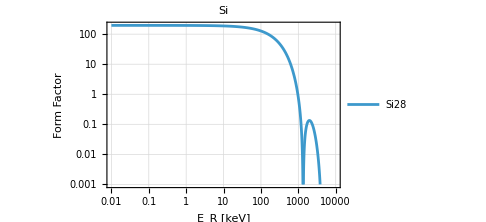
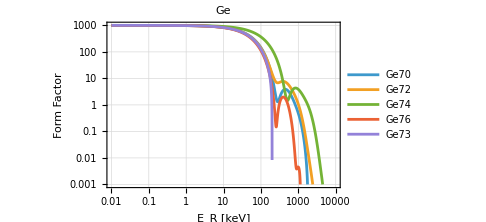
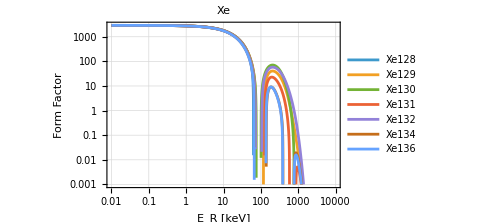
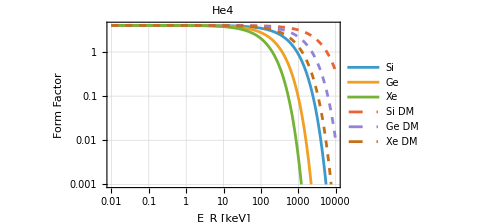

```mathematica
targetisotope = "Si28";

nucleiformfactors = Table[plt = 
LogLogPlot[
	Table[FM[targetisotope][p,p][(qfunc[10^-6 er,mT[targetisotope]]by[Anum[targetisotope]]/2)^2]
		,{targetisotope,isotopes[nuclei]}]//Evaluate,
	{er, 10^-2,10^4},
	PlotLegends->{isotopes[nuclei]}, 
	FrameLabel->{"E_R [keV]","Form Factor"},
	ImageSize->Medium,
	PlotRange->{Automatic,{10^-3,Automatic}},
	PlotLabel->nuclei]//frametrick;
(*Export[FileNameJoin[{plotdir,StringJoin[nuclei,"_form_factors.pdf"]}],plt];*)
plt,
{nuclei,{"Si","Ge","Xe"}}];

formfactors = Row[Flatten[{nucleiformfactors,heFF}],Spacer[2]]
```

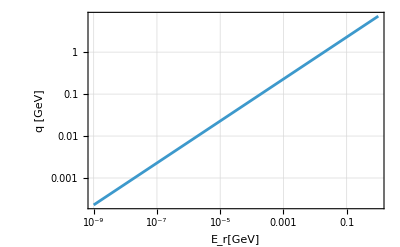

```mathematica
LogLogPlot[qfunc[er,mT["Si28"]],{er, 10^-9,1}, FrameLabel->{"E_r[GeV]", "q [GeV]"}]//frametrick
```

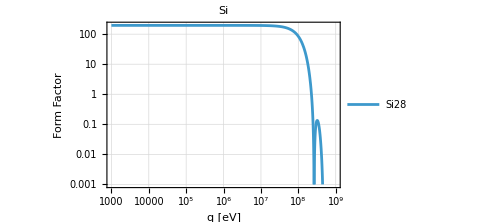
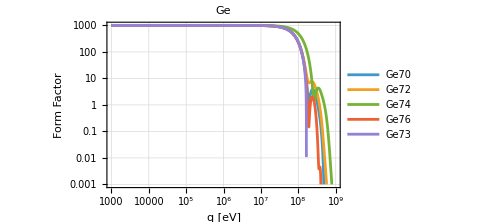
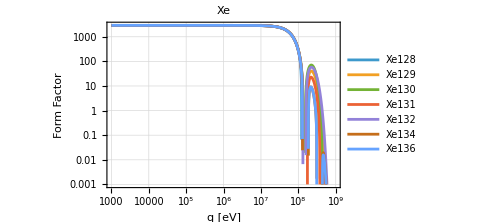

```mathematica
nucleiformfactorsq = Table[plt = 
LogLogPlot[
Table[FM[targetisotope][p,p][(10^-9 q by[Anum[targetisotope]]/2)^2],{targetisotope,isotopes[nuclei]}]//Evaluate,{q, 10^3,10^9},
PlotLegends->{isotopes[nuclei]}, FrameLabel->{"q [eV]","Form Factor"},ImageSize->Medium,PlotRange->{Automatic,{10^-3,Automatic}},PlotLabel->nuclei]//frametrick;
(*Export[FileNameJoin[{plotdir,StringJoin[nuclei,"_form_factors.pdf"]}],plt];*)
plt,
{nuclei,{"Si","Ge","Xe"}}];

Row[Flatten[{nucleiformfactorsq}],Spacer[2]]
```

a1 = 20.2933, b1 = 3.92820, a2 = 19.0298, b2 = 0.344000, a3 = 8.97670, b3 = 26.4659, a4 = 1.99000, b4 = 64.2658, and c = 3.71180 .

```mathematica
hbartest = Quantity[, "ReducedPlanckConstant"];
gev = Quantity[1,"GeV"];
cqu = Quantity[cval,"m"/"s"];
ang = Quantity[1 ,"Angstrom"];
hbarval =  UnitConvert[hbartest,"SIBase"];
ang2invGev = QuantityMagnitude[UnitConvert[ang/(cqu hbarval), 1/"GeV"]];
GeV2anginv = QuantityMagnitude[UnitConvert[gev/(cqu hbarval) ,1/"Angstroms"]];
```

Quantity::unkunit: Unable to interpret unit specification Angstrom.

### Baryon

```mathematica
target = "Xe" ;

differentialratelabels = {"E_R [keV]","dR_T/dE_R [events/(day kg keV)]"};

	
(* this function loops over the different target nuclei to give the rate*)
rateplotovertargets[DMtype_,targetOp_,targets_] := Module[{mass,charge,title},
	If[DMtype =="neutron",
		mass = mdarkneutron;
		charge = Qneutron;
		title = "Dark Neutron"
		,
		
		mass = mdarkneutron;
		charge = 1;
		title = "Dark Proton"];
	kappa = 10^-9;

	LogLogPlot[
		Table[10^-6 dRTdEr[targetOp,target,10^-6 Er][mass,rsquare["lattice",mass ],charge,kappa],{target,targets}]//Evaluate,
				{Er,  10^-2,100 },
		FrameLabel->differentialratelabels,
		PlotLabel->StringJoin[title,", κ=10^-9, Dark Baryon Mass "<>ToString[mdarkneutron]<> " GeV"], 
		PlotLegends->targets 
		]//frametrick
	]
```

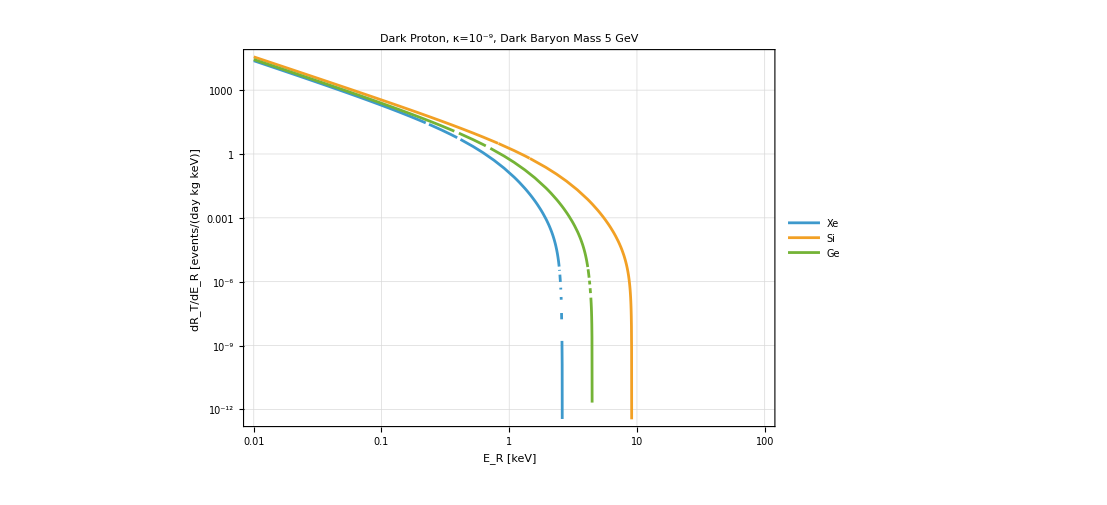

```mathematica
rateplotovertargets["proton", "MC",{"Xe","Si","Ge"}]
```

```mathematica
(*data takes a minute to generate, refine the step size as needed*)
target = "Xe";
QDM = 1;
kappa = 1;
mtab = Table[{10^log10mDM, RTintegratedhalo["MC",target][10^log10mDM,rsq,QDM, kappa]},{log10mDM,Range[0,3,0.1]}];
```

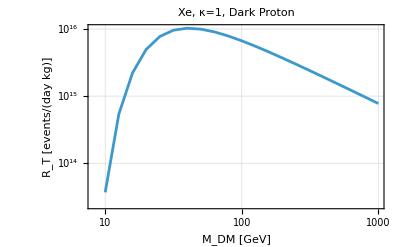

```mathematica
ListLogLogPlot[mtab,
	FrameLabel->{"M_DM [GeV]","R_T [events/(day kg)]"},
	PlotLabel->StringJoin[target,", κ=1, Dark Proton"]
	,Joined->True]//frametrick
```

```mathematica
target = "Si";
kappa = 10^-9;
HaloTab = Table[{10^log10mDM, RTintegratedhalo["MC",target][10^log10mDM,rsq,QDM, kappa]},{log10mDM,Range[0,3,0.1]}];
DiskTab = Table[{10^log10mDM, RTintegrateddisk["MC",target][10^log10mDM,rsq,QDM, kappa]},{log10mDM,Range[0,3,0.1]}];
```

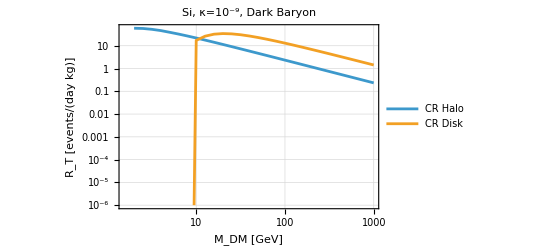

```mathematica
ListLogLogPlot[{HaloTab, DiskTab},
	FrameLabel->{"M_DM [GeV]","R_T [events/(day kg)]"},
	PlotLabel->StringJoin[target,", κ=10^-9, Dark Baryon"], 
	PlotLegends->{"CR Halo","CR Disk"},
	Joined->True,
	PlotRange->{Automatic, {10^-6,Automatic}}
	]//frametrick
```